```mathematica
Quit[];
```

## Near - bdry expansion

```mathematica
coord = {u,t,xL,xP1,xP2};

$Assumptions= And[u∈Reals,u>0,Σ[t,u]>0];

metricsign=-1;
```

```mathematica
metric=({{0, -1/u^2, 0, 0, 0}, {-1/u^2, -A[t,u], 0, 0, 0}, {0, 0, Σ[t,u]^2 Exp[-2B[t,u]], 0, 0}, {0, 0, 0, Σ[t,u]^2 Exp[B[t,u]], 0}, {0, 0, 0, 0, Σ[t,u]^2 Exp[B[t,u]]}});
```

```mathematica
<<diffgeo.m;
```

```mathematica
EinsteinEqns=RicciTensor+4metric//Simplify//Expand;
```

```mathematica
Eoms=Drop[Union[Flatten[EinsteinEqns]],1];
```

```mathematica
ord=5;
```

```mathematica
AS[t_,u_]=1/u^2(1+Sum[Subscript[ASc, i][t] u^i,{i,1,ord}]);
ΣS[t_,u_]=1/u(1+Sum[Subscript[ΣSc, i][t] u^i,{i,1,ord}]);
BS[t_,u_]=Sum[Subscript[BSc, i][t] u^i,{i,1,ord}];
```

```mathematica
subsS={A->AS,Σ->ΣS,B->BS};
```

```mathematica
EomsS=(Expand/@Series[#,{u,0,ord}])&/@(u^2 Eoms//.subsS);
```

```mathematica
sc[eqnum_,ordnum_]:=SeriesCoefficient[EomsS⟦eqnum⟧,ordnum]
```

```mathematica
r Series[1/(r+f[t]),{r,∞,2}]
```

1-f[t]/r+O[1/r]^2

```mathematica
Subscript[ΣSc, 1][t_]=-f[t];
```

```mathematica
sol=Flatten[Solve[{sc[2,1]==0,sc[3,1]==0},{Subscript[BSc, 1][t],Subscript[ASc, 1][t]}]];
Subscript[ASc, 1][t_]=Subscript[ASc, 1][t]/.sol;
Subscript[BSc, 1][t_]=Subscript[BSc, 1][t]/.sol;
sol=.
```

```mathematica
i=2;
sol=Flatten[Solve[{sc[2,i]==0,sc[3,i]==0,sc[4,i]==0},{Subscript[BSc, i][t],Subscript[ASc, i][t],Subscript[ΣSc, i][t]}]];
Subscript[ASc, i][t_]=Subscript[ASc, i][t]/.sol;
Subscript[BSc, i][t_]=Subscript[BSc, i][t]/.sol;
Subscript[ΣSc, i][t_]=Subscript[ΣSc, i][t]/.sol;
sol=.
i=.
```

```mathematica
i=3;
sol=Flatten[Solve[{sc[2,i]==0,sc[3,i]==0,sc[4,i]==0},{Subscript[BSc, i][t],Subscript[ASc, i][t],Subscript[ΣSc, i][t]}]];
Subscript[ASc, i][t_]=Subscript[ASc, i][t]/.sol;
Subscript[BSc, i][t_]=Subscript[BSc, i][t]/.sol;
Subscript[ΣSc, i][t_]=Subscript[ΣSc, i][t]/.sol;
sol=.
i=.
```

```mathematica
Subscript[ΣSc, 4][t_]=Subscript[ΣSc, 4][t]//.Solve[sc[1,4]==0,Subscript[ΣSc, 4][t]]⟦1⟧
```

0

```mathematica
Table[sc[i,4]//Expand,{i,1,5}]
```

{0,0,0,0,0}

```mathematica
i=5;
sol=Flatten[Solve[{sc[2,i]==0,sc[3,i]==0,sc[4,i]==0},{Subscript[BSc, i][t],Subscript[ASc, i][t],Subscript[ΣSc, i][t]}]];
Subscript[ASc, i][t_]=Subscript[ASc, i][t]/.sol;
Subscript[BSc, i][t_]=Subscript[BSc, i][t]/.sol;
Subscript[ΣSc, i][t_]=Subscript[ΣSc, i][t]/.sol;
sol=.
i=.
```

```mathematica
Table[sc[i,5]//Expand,{i,1,5}]
```

{0,0,0,0,-3/2 ASc_4'[t]}

```mathematica
Subscript[ASc, 4][t_]=a4;
```

```mathematica
AS[t,u]
```

(1+a4 u^4-2 u f[t]+2 a4 u^5 f[t]+u^2 (f[t]^2+2 f'[t]))/u^2

```mathematica
BS[t,u]
```

BS[t,u]

```mathematica
ΣS[t,u]
```

ΣS[t,u]

```mathematica
feq0[t_]=0;
```

```mathematica
feq0[t_,u_]=0;
```

```mathematica
AS[t,u]//.f->feq0//Expand
```

AS[t,u]

```mathematica
BS[t,u]//.f->feq0//Expand
```

BS[t,u]

```mathematica
ΣS[t,u]//.f->feq0//Expand
```

ΣS[t,u]

## Equations of motion

```mathematica
subsΣdot=Solve[Derivative[1,0][Σ][t,u]-1/2 u^2 A[t,u]Derivative[0,1][Σ][t,u]==Σdot[t,u],Derivative[1,0][Σ][t,u]]⟦1⟧//Expand
```

{Σ^(1,0)[t,u]→Σdot[t,u]+1/2 u^2 A[t,u] Σ^(0,1)[t,u]}

```mathematica
subsΣdot/.Rule->Equal
```

{Σ^(1,0)[t,u]==Σdot[t,u]+1/2 u^2 A[t,u] Σ^(0,1)[t,u]}

```mathematica
DSolve[{Derivative[1,0][Σ][t,u]==Σdot[t,u]+1/2 u^2 A[t,u] Derivative[0,1][Σ][t,u]},{Σ[t,u],Σ[t,u]},{t}]
```

{{Σ[t,u]→C[1]+1/2 (2 Σdot[K[1],u]+u^2 A[K[1],u] Σ^(0,1)[K[1],u])K[1]1t}}

```mathematica
Simplify[{{Σ[t,u]->C[1]+1/2 (2 Σdot[K[1],u]+u^2 A[K[1],u] Derivative[0,1][Σ][K[1],u])K[1]1t}}]
```

{{Σ[t,u]→C[1]+(Σdot[K[1],u]+1/2 u^2 A[K[1],u] Σ^(0,1)[K[1],u])K[1]1t}}

```mathematica
{{Σ[t,u]->C[1]+(Σdot[K[1],u]+1/2 u^2 A[K[1],u] Derivative[0,1][Σ][K[1],u])K[1]1t}}/.Rule->Equal
```

{{Σ[t,u]==C[1]+(Σdot[K[1],u]+1/2 u^2 A[K[1],u] Σ^(0,1)[K[1],u])K[1]1t}}

```mathematica
Flatten[{{Σ[t,u]==C[1]+(Σdot[K[1],u]+1/2 u^2 A[K[1],u] Derivative[0,1][Σ][K[1],u])K[1]1t}}]
```

{Σ[t,u]==C[1]+(Σdot[K[1],u]+1/2 u^2 A[K[1],u] Σ^(0,1)[K[1],u])K[1]1t}

```mathematica
First[{Σ[t,u]==C[1]+(Σdot[K[1],u]+1/2 u^2 A[K[1],u] Derivative[0,1][Σ][K[1],u])K[1]1t}]
```

Σ[t,u]==C[1]+(Σdot[K[1],u]+1/2 u^2 A[K[1],u] Σ^(0,1)[K[1],u])K[1]1t

```mathematica
Activate[Σ[t,u]==C[1]+(Σdot[K[1],u]+1/2 u^2 A[K[1],u] Derivative[0,1][Σ][K[1],u])K[1]1t,Unevaluated[Integrate]]
```

Σ[t,u]==C[1]+∫_1^t (Σdot[K[1],u]+1/2 u^2 A[K[1],u] Σ^(0,1)[K[1],u])ⅆK[1]

```mathematica
Solve[Σ[t,u]==C[1]+∫_1^t (Σdot[K[1],u]+1/2 u^2 A[K[1],u] Derivative[0,1][Σ][K[1],u])ⅆK[1],{t},Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[Σ[t,u]==C[1]+∫_1^t (Σdot[K[1],u]+1/2 u^2 A[K[1],u] Σ^(0,1)[K[1],u])ⅆK[1],{t},ℝ]

```mathematica
subsdots={#,D[#,u]}&/@Union[subsΣdot,subsΣdot/.{Σ->B,Σdot->Bdot}]//Flatten
```

{B^(1,0)[t,u]→Bdot[t,u]+1/2 u^2 A[t,u] B^(0,1)[t,u],B^(1,1)[t,u]→u A[t,u] B^(0,1)[t,u]+1/2 u^2 A^(0,1)[t,u] B^(0,1)[t,u]+Bdot^(0,1)[t,u]+1/2 u^2 A[t,u] B^(0,2)[t,u],Σ^(1,0)[t,u]→Σdot[t,u]+1/2 u^2 A[t,u] Σ^(0,1)[t,u],Σ^(1,1)[t,u]→u A[t,u] Σ^(0,1)[t,u]+1/2 u^2 A^(0,1)[t,u] Σ^(0,1)[t,u]+Σdot^(0,1)[t,u]+1/2 u^2 A[t,u] Σ^(0,2)[t,u]}

```mathematica
{Derivative[1,0][B][t,u],Derivative[1,0][Σ][t,u],Derivative[1,1][B][t,u],Derivative[1,1][Σ][t,u]}/.subsdots
```

{Bdot[t,u]+1/2 u^2 A[t,u] B^(0,1)[t,u],Σdot[t,u]+1/2 u^2 A[t,u] Σ^(0,1)[t,u],u A[t,u] B^(0,1)[t,u]+1/2 u^2 A^(0,1)[t,u] B^(0,1)[t,u]+Bdot^(0,1)[t,u]+1/2 u^2 A[t,u] B^(0,2)[t,u],u A[t,u] Σ^(0,1)[t,u]+1/2 u^2 A^(0,1)[t,u] Σ^(0,1)[t,u]+Σdot^(0,1)[t,u]+1/2 u^2 A[t,u] Σ^(0,2)[t,u]}

```mathematica
Permutations[%11]
```

{ΣS[t,u],ΣS[u,t]}

```mathematica
MatrixForm[%12]
```

(Σ^(1,0)[t,u]→Σdot[t,u]+1/2 u^2 A[t,u] Σ^(0,1)[t,u])

```mathematica
Transpose[%13]
```

{Σ^(1,0)[t,u]==Σdot[t,u]+1/2 u^2 A[t,u] Σ^(0,1)[t,u]}

```mathematica
Dimensions[%14]
```

{1,1}

```mathematica
Times@@{4,24}
```

96

```mathematica
BaseForm[96,2]
```

1100000_2

```mathematica
FactorInteger[96]
```

{{2,5},{3,1}}

```mathematica
Times@@Power@@@{{2,5},{3,1}}
```

96

```mathematica
subsundots=Flatten[Solve[ReplacePart[#,0->Equal],#⟦2⟧//.A->feq0]&/@subsdots]//Expand
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[subsdots].

Flatten[subsdots]

```mathematica
{Bdot[t,u]->-1/2 u^2 A[t,u] Derivative[0,1][B][t,u]+Derivative[1,0][B][t,u],Derivative[0,1][Bdot][t,u]->-u A[t,u] Derivative[0,1][B][t,u]-1/2 u^2 Derivative[0,1][A][t,u] Derivative[0,1][B][t,u]-1/2 u^2 A[t,u] Derivative[0,2][B][t,u]+Derivative[1,1][B][t,u],Σdot[t,u]->-1/2 u^2 A[t,u] Derivative[0,1][Σ][t,u]+Derivative[1,0][Σ][t,u],Derivative[0,1][Σdot][t,u]->-u A[t,u] Derivative[0,1][Σ][t,u]-1/2 u^2 Derivative[0,1][A][t,u] Derivative[0,1][Σ][t,u]-1/2 u^2 A[t,u] Derivative[0,2][Σ][t,u]+Derivative[1,1][Σ][t,u]}
```

{Bdot[t,u]→-1/2 u^2 A[t,u] B^(0,1)[t,u]+B^(1,0)[t,u],Bdot^(0,1)[t,u]→-u A[t,u] B^(0,1)[t,u]-1/2 u^2 A^(0,1)[t,u] B^(0,1)[t,u]-1/2 u^2 A[t,u] B^(0,2)[t,u]+B^(1,1)[t,u],Σdot[t,u]→-1/2 u^2 A[t,u] Σ^(0,1)[t,u]+Σ^(1,0)[t,u],Σdot^(0,1)[t,u]→-u A[t,u] Σ^(0,1)[t,u]-1/2 u^2 A^(0,1)[t,u] Σ^(0,1)[t,u]-1/2 u^2 A[t,u] Σ^(0,2)[t,u]+Σ^(1,1)[t,u]}

```mathematica
eq1=Expand[Σ[t,u]Eoms⟦1⟧]//.subsdots//Expand
```

-3/2 Σ[t,u] (B^(0,1)[t,u])^2-(6 Σ^(0,1)[t,u])/u-3 Σ^(0,2)[t,u]

```mathematica
eq2=Expand[Σ[t,u]Eoms⟦2⟧]//.subsdots//Expand
```

-(4 Σ[t,u])/u^2+u Σ[t,u] A^(0,1)[t,u]-3/2 Bdot[t,u] Σ[t,u] B^(0,1)[t,u]-3/4 u^2 A[t,u] Σ[t,u] (B^(0,1)[t,u])^2-3 u A[t,u] Σ^(0,1)[t,u]-3 Σdot^(0,1)[t,u]+1/2 u^2 Σ[t,u] A^(0,2)[t,u]-3/2 u^2 A[t,u] Σ^(0,2)[t,u]

```mathematica
eq3=Expand[1/Σ[t,u] ⅇ^(2 B[t,u])Eoms⟦3⟧]//.subsdots//Expand
```

4 Σ[t,u]-3 u^2 Σdot[t,u] B^(0,1)[t,u]-2 u^2 Σ[t,u] Bdot^(0,1)[t,u]-3 u^2 Bdot[t,u] Σ^(0,1)[t,u]+(4 u^2 Σdot[t,u] Σ^(0,1)[t,u])/Σ[t,u]+2 u^2 Σdot^(0,1)[t,u]

```mathematica
eq4=Expand[1/Σ[t,u] ⅇ^(-B[t,u])Eoms⟦4⟧]//.subsdots//Expand
```

4 Σ[t,u]+3/2 u^2 Σdot[t,u] B^(0,1)[t,u]+u^2 Σ[t,u] Bdot^(0,1)[t,u]+3/2 u^2 Bdot[t,u] Σ^(0,1)[t,u]+(4 u^2 Σdot[t,u] Σ^(0,1)[t,u])/Σ[t,u]+2 u^2 Σdot^(0,1)[t,u]

```mathematica
eq5=Expand[Σ[t,u]Eoms⟦5⟧]//.subsdots//Expand
```

-4 A[t,u] Σ[t,u]-3/2 Bdot[t,u]^2 Σ[t,u]+u^3 A[t,u] Σ[t,u] A^(0,1)[t,u]-3/2 u^2 Σdot[t,u] A^(0,1)[t,u]-3/2 u^2 A[t,u] Bdot[t,u] Σ[t,u] B^(0,1)[t,u]-3/8 u^4 A[t,u]^2 Σ[t,u] (B^(0,1)[t,u])^2+3/4 u^4 A[t,u] A^(0,1)[t,u] Σ^(0,1)[t,u]+1/2 u^4 A[t,u] Σ[t,u] A^(0,2)[t,u]+3/2 u^2 Σ^(0,1)[t,u] A^(1,0)[t,u]-3 Σ^(2,0)[t,u]

```mathematica
eq4Σ=eq1
```

-3/2 Σ[t,u] (B^(0,1)[t,u])^2-(6 Σ^(0,1)[t,u])/u-3 Σ^(0,2)[t,u]

```mathematica
eq5
```

-4 A[t,u] Σ[t,u]-3/2 Bdot[t,u]^2 Σ[t,u]+u^3 A[t,u] Σ[t,u] A^(0,1)[t,u]-3/2 u^2 Σdot[t,u] A^(0,1)[t,u]-3/2 u^2 A[t,u] Bdot[t,u] Σ[t,u] B^(0,1)[t,u]-3/8 u^4 A[t,u]^2 Σ[t,u] (B^(0,1)[t,u])^2+3/4 u^4 A[t,u] A^(0,1)[t,u] Σ^(0,1)[t,u]+1/2 u^4 A[t,u] Σ[t,u] A^(0,2)[t,u]+3/2 u^2 Σ^(0,1)[t,u] A^(1,0)[t,u]-3 Σ^(2,0)[t,u]

```mathematica
eq4Bdot=2/(9 u^2)(eq4-eq3)//Expand
```

Σdot[t,u] B^(0,1)[t,u]+2/3 Σ[t,u] Bdot^(0,1)[t,u]+Bdot[t,u] Σ^(0,1)[t,u]

```mathematica
eq4Σdot=eq3//.Solve[eq4Bdot==0,Derivative[0,1][Bdot][t,u]]⟦1⟧//Expand
```

4 Σ[t,u]+(4 u^2 Σdot[t,u] Σ^(0,1)[t,u])/Σ[t,u]+2 u^2 Σdot^(0,1)[t,u]

```mathematica
eq4A=1/Σ[t,u] eq2//.Solve[eq1==0,Derivative[0,2][Σ][t,u]]⟦1⟧//Expand
```

-4/u^2+u A^(0,1)[t,u]-3/2 Bdot[t,u] B^(0,1)[t,u]-(3 Σdot^(0,1)[t,u])/Σ[t,u]+1/2 u^2 A^(0,2)[t,u]

```mathematica
Σdoteval[t_,u_]=Σdot[t,u]//.Solve[subsΣdot⟦1⟧⟦2⟧==Derivative[1,0][Σ][t,u],Σdot[t,u]]⟦1⟧//Expand
```

-1/2 u^2 A[t,u] Σ^(0,1)[t,u]+Σ^(1,0)[t,u]

```mathematica
Bdoteval[t_,u_]=Expand[Σdot[t,u]//.Solve[subsΣdot⟦1⟧⟦2⟧==Derivative[1,0][Σ][t,u],Σdot[t,u]]⟦1⟧]//.Σ->B
```

-1/2 u^2 A[t,u] B^(0,1)[t,u]+B^(1,0)[t,u]

```mathematica
ΣdotS[t_,u_]=Σdoteval[t,u]//.Union[subsS,{f->feq0}]//Expand
```

1/(2 u^2)+(a4 u^2)/2

```mathematica
BdotS[t_,u_]=Σdoteval[t,u]//.Union[{Σ->B},subsS,{f->feq0}]//Expand
```

-2 u^3 BSc_4[t]-2 a4 u^7 BSc_4[t]-3/2 u^4 BSc_4'[t]-5/2 a4 u^8 BSc_4'[t]+u^5 BSc_4''[t]

## Warp - factors redefinitions

```mathematica
Aredef[t_,u_]=1/u^2+u Areg[t,u];  (*where do the scaling factors for the reg expressions come from*)
Bredef[t_,u_]=u^3 Breg[t,u];
Σredef[t_,u_]=1/u+u^2 Σreg[t,u];
```

```mathematica
Σdotredef[t_,u_]=1/(2 u^2)+1/2 u^2 Σdotreg[t,u];
Bdotredef[t_,u_]=-2 u^3 Bdotreg[t,u];
```

```mathematica
subsredef={A->Aredef,B->Bredef,Σ->Σredef,Σdot->Σdotredef,Bdot->Bdotredef};
```

```mathematica
eq4Σredef=-1/(3 u^2)eq4Σ//.subsredef//Expand
```

9/2 u Breg[t,u]^2+(6 Σreg[t,u])/u^2+9/2 u^4 Breg[t,u]^2 Σreg[t,u]+3 u^2 Breg[t,u] Breg^(0,1)[t,u]+3 u^5 Breg[t,u] Σreg[t,u] Breg^(0,1)[t,u]+1/2 u^3 (Breg^(0,1)[t,u])^2+1/2 u^6 Σreg[t,u] (Breg^(0,1)[t,u])^2+(6 Σreg^(0,1)[t,u])/u+Σreg^(0,2)[t,u]

```mathematica
eq4ΣredefSRC=eq4Σredef//.Σreg->feq0
```

9/2 u Breg[t,u]^2+3 u^2 Breg[t,u] Breg^(0,1)[t,u]+1/2 u^3 (Breg^(0,1)[t,u])^2

```mathematica
eq4ΣredefKIN=Collect[eq4Σredef-eq4ΣredefSRC,{Σreg[t,u],Derivative[0,1][Σreg][t,u],Derivative[0,2][Σreg][t,u]}]
```

Σreg[t,u] (6/u^2+9/2 u^4 Breg[t,u]^2+3 u^5 Breg[t,u] Breg^(0,1)[t,u]+1/2 u^6 (Breg^(0,1)[t,u])^2)+(6 Σreg^(0,1)[t,u])/u+Σreg^(0,2)[t,u]

```mathematica
eq4Σdotredef=1/u^4 eq4Σdot//.subsredef//Expand
```

2/u^5+(2 Σdotreg[t,u])/u+(4 Σreg[t,u])/u^2-2/(u^6 (1/u+u^2 Σreg[t,u]))-(2 Σdotreg[t,u])/(u^2 (1/u+u^2 Σreg[t,u]))+(4 Σreg[t,u])/(u^3 (1/u+u^2 Σreg[t,u]))+(4 u Σdotreg[t,u] Σreg[t,u])/(1/u+u^2 Σreg[t,u])+Σdotreg^(0,1)[t,u]+(2 Σreg^(0,1)[t,u])/(u^2 (1/u+u^2 Σreg[t,u]))+(2 u^2 Σdotreg[t,u] Σreg^(0,1)[t,u])/(1/u+u^2 Σreg[t,u])

```mathematica
eq4ΣdotredefSRC=eq4Σdotredef//.Σdotreg->feq0//Simplify
```

(2 (5 Σreg[t,u]+2 u^3 Σreg[t,u]^2+u Σreg^(0,1)[t,u]))/(u^2+u^5 Σreg[t,u])

```mathematica
eq4ΣdotredefKIN=Simplify/@Collect[eq4Σdotredef-eq4ΣdotredefSRC//Simplify,{Σdotreg[t,u],Derivative[0,1][Σdotreg][t,u]}]
```

Σdotreg^(0,1)[t,u]+(2 u^2 Σdotreg[t,u] (3 Σreg[t,u]+u Σreg^(0,1)[t,u]))/(1+u^3 Σreg[t,u])

```mathematica
eq4Bdotredef=Expand[1/(-4/3 u^3 Σ[t,u])eq4Bdot]//.subsredef//Expand
```

(3 Bdotreg[t,u])/u-(3 Bdotreg[t,u])/(2 u^2 (1/u+u^2 Σreg[t,u]))-(9 Breg[t,u])/(8 u^3 (1/u+u^2 Σreg[t,u]))-(9 u Breg[t,u] Σdotreg[t,u])/(8 (1/u+u^2 Σreg[t,u]))+(3 u Bdotreg[t,u] Σreg[t,u])/(1/u+u^2 Σreg[t,u])+Bdotreg^(0,1)[t,u]-(3 Breg^(0,1)[t,u])/(8 u^2 (1/u+u^2 Σreg[t,u]))-(3 u^2 Σdotreg[t,u] Breg^(0,1)[t,u])/(8 (1/u+u^2 Σreg[t,u]))+(3 u^2 Bdotreg[t,u] Σreg^(0,1)[t,u])/(2 (1/u+u^2 Σreg[t,u]))

```mathematica
eq4BdotredefSRC=eq4Bdotredef//.Bdotreg->feq0//Simplify
```

-(3 (1+u^4 Σdotreg[t,u]) (3 Breg[t,u]+u Breg^(0,1)[t,u]))/(8 u^2 (1+u^3 Σreg[t,u]))

```mathematica
eq4BdotredefKIN=Simplify/@Collect[eq4Bdotredef-eq4BdotredefSRC//Simplify,{Bdotreg[t,u],Derivative[0,1][Bdotreg][t,u]}]
```

Bdotreg^(0,1)[t,u]+(3 Bdotreg[t,u] (1+4 u^3 Σreg[t,u]+u^4 Σreg^(0,1)[t,u]))/(2 (u+u^4 Σreg[t,u]))

```mathematica
eq4Aredef=2/u^3 eq4A//.Union[subsredef,Solve[eq4Σdotredef==0,Derivative[0,1][Σdotreg][t,u]]⟦1⟧]//Expand
```

-6/u^5+(2 Areg[t,u])/u^2+18 u^2 Bdotreg[t,u] Breg[t,u]-6/(u^7 (1/u+u^2 Σreg[t,u])^2)-(6 Σdotreg[t,u])/(u^3 (1/u+u^2 Σreg[t,u])^2)+(12 Σreg[t,u])/(u^4 (1/u+u^2 Σreg[t,u])^2)+(12 Σdotreg[t,u] Σreg[t,u])/((1/u+u^2 Σreg[t,u])^2)+12/(u^6 (1/u+u^2 Σreg[t,u]))+(12 Σreg[t,u])/(u^3 (1/u+u^2 Σreg[t,u]))+(4 Areg^(0,1)[t,u])/u+6 u^3 Bdotreg[t,u] Breg^(0,1)[t,u]+(6 Σreg^(0,1)[t,u])/(u^3 (1/u+u^2 Σreg[t,u])^2)+(6 u Σdotreg[t,u] Σreg^(0,1)[t,u])/((1/u+u^2 Σreg[t,u])^2)+Areg^(0,2)[t,u]

```mathematica
eq4AredefSRC=eq4Aredef//.{Areg->feq0}//FullSimplify
```

1/((u+u^4 Σreg[t,u])^2)6 (Σreg[t,u] (4+u^3 Σreg[t,u])+u^4 Bdotreg[t,u] (1+u^3 Σreg[t,u])^2 (3 Breg[t,u]+u Breg^(0,1)[t,u])+u Σreg^(0,1)[t,u]+u Σdotreg[t,u] (-1+2 u^3 Σreg[t,u]+u^4 Σreg^(0,1)[t,u]))

```mathematica
eq4AredefKIN=eq4Aredef-eq4AredefSRC//Simplify
```

(2 Areg[t,u])/u^2+(4 Areg^(0,1)[t,u])/u+Areg^(0,2)[t,u]

## Solving a set of linear equations

```mathematica
subslists={Σreg[t,u]->Σreglist,Derivative[0,1][Σreg][t,u]->ΣregDlist,Breg[t,u]->Breglist,Derivative[0,1][Breg][t,u]->BregDlist,Σdotreg[t,u]->Σdotreglist,Bdotreg[t,u]->Bdotreglist,u->ulist,Areg[t,u]->Areglist};
```

```mathematica
eq4ΣredefKIN//.subslists
```

(6 ΣregDlist)/ulist+(6/ulist^2+(9 Breglist^2 ulist^4)/2+3 BregDlist Breglist ulist^5+(BregDlist^2 ulist^6)/2) Σreglist+Σreg^(0,2)[t,ulist]

```mathematica
obtainΣreglist[Breglist_,BregDlist_]:=Module[{bVEC,aMAT,bVECbc,res},

bVEC={Quiet[Rest[-(9 Breglist^2 zlist)/2-3 BregDlist Breglist zlist^2-(BregDlist^2 zlist^3)/2]],Table[0,{Ncut}]}//Flatten;

aMAT={
{Dm0+DiagonalMatrix[Quiet[Rest[6 zlist^-1]]], DiagonalMatrix[Quiet[Rest[6/zlist^2+(9 Breglist^2 zlist^4)/2+3 BregDlist Breglist zlist^5+(BregDlist^2 zlist^6)/2]]]},
{-IdentityMatrix[Ncut], Dm0}
} //ArrayFlatten;

bVECbc = N[{0 dCOL, 0 dCOL} //Flatten,numPREC];

bVEC = N[bVEC - bVECbc,numPREC];

res = LinearSolve[aMAT,bVEC]//Expand;

{Prepend[res⟦Ncut+1;;2Ncut⟧,0],Prepend[res⟦1;;Ncut⟧,0]} (*constructs a matrix where the two rows correpond to the two vectors *) 

]
```

```mathematica
eq4ΣdotredefKIN//.subslists
```

(2 ulist^2 Σdotreglist (ulist ΣregDlist+3 Σreglist))/(1+ulist^3 Σreglist)+Σdotreg^(0,1)[t,ulist]

```mathematica
-eq4ΣdotredefSRC//.subslists
```

-(2 (ulist ΣregDlist+5 Σreglist+2 ulist^3 Σreglist^2))/(ulist^2+ulist^5 Σreglist)

```mathematica
obtainΣdotreglist[Σreglist_,ΣregDlist_]:=Module[{bVEC,bc,aMAT,bVECbc,res},

bc=-1; (*is this Subscript[a, 4]=-1 as they write in their paper? *)

aMAT=Dm0+DiagonalMatrix[Quiet[Rest[(2 zlist^2 (zlist ΣregDlist+3 Σreglist))/(1+zlist^3 Σreglist)]]];

bVEC=Quiet[Rest[-(2 (zlist ΣregDlist+5 Σreglist+2 zlist^3 Σreglist^2))/(zlist^2+zlist^5 Σreglist)]];

bVECbc = bc dCOL;

bVEC = N[bVEC - bVECbc,numPREC];

res = LinearSolve[aMAT,bVEC]//Expand;

Prepend[res,bc]

]
```

```mathematica
eq4BdotredefKIN//.subslists
```

(3 Bdotreglist (1+ulist^4 ΣregDlist+4 ulist^3 Σreglist))/(2 (ulist+ulist^4 Σreglist))+Bdotreg^(0,1)[t,ulist]

```mathematica
-eq4BdotredefSRC//.subslists
```

(3 (3 Breglist+BregDlist ulist) (1+ulist^4 Σdotreglist))/(8 ulist^2 (1+ulist^3 Σreglist))

```mathematica
obtainBdotreglist[Σreglist_,ΣregDlist_,Breglist_,BregDlist_,Σdotreglist_]:=Module[{bc,bVEC,aMAT,bVECbc,res},

bc=First[BregDlist];
aMAT=Dm0+DiagonalMatrix[Quiet[Rest[(3 (1+zlist^4 ΣregDlist+4 zlist^3 Σreglist))/(2 (zlist+zlist^4 Σreglist))]]];

bVEC=Quiet[Rest[(3 (3 Breglist+BregDlist zlist) (1+zlist^4 Σdotreglist))/(8 zlist^2 (1+zlist^3 Σreglist))]];

bVECbc = bc dCOL;

bVEC = N[bVEC - bVECbc,numPREC];

res = LinearSolve[aMAT,bVEC]//Expand;

Prepend[res,bc]

];
```

```mathematica
eq4AredefKIN
```

(2 Areg[t,u])/u^2+(4 Areg^(0,1)[t,u])/u+Areg^(0,2)[t,u]

```mathematica
-eq4AredefSRC//.subslists
```

-(6 (ulist ΣregDlist+Bdotreglist ulist^4 (3 Breglist+BregDlist ulist) (1+ulist^3 Σreglist)^2+Σreglist (4+ulist^3 Σreglist)+ulist Σdotreglist (-1+ulist^4 ΣregDlist+2 ulist^3 Σreglist)))/(ulist+ulist^4 Σreglist)^2

```mathematica
obtainAreglist[Breglist_,BregDlist_,Σreglist_,ΣregDlist_,Bdotreglist_,Σdotreglist_]:=Module[{bc1,bc0,bVEC,aMAT,bVECbc,res},


bc1=-1;
bc0=0;


bVEC={Quiet[Rest[-1/((zlist+zlist^4 Σreglist)^2)6 (zlist ΣregDlist+Bdotreglist zlist^4 (3 Breglist+BregDlist zlist) (1+zlist^3 Σreglist)^2+Σreglist (4+zlist^3 Σreglist)+zlist Σdotreglist (-1+zlist^4 ΣregDlist+2 zlist^3 Σreglist))]],Table[0,{Ncut}]}//Flatten;

aMAT={
{Dm0+DiagonalMatrix[Quiet[Rest[4 zlist^-1]]], DiagonalMatrix[Quiet[Rest[2/zlist^2]]]},
{-IdentityMatrix[Ncut], Dm0}
} //ArrayFlatten;

bVECbc = N[{bc1 dCOL, bc0 dCOL} //Flatten,numPREC];

bVEC = N[bVEC - bVECbc,numPREC];

res = LinearSolve[aMAT,bVEC]//Expand;

Prepend[res⟦Ncut+1;;2Ncut⟧,bc0]

]
```

```mathematica
Bregteval[t_,u_]=Derivative[1,0][Breg][t,u]//.Solve[(Bdoteval[t, u] //. subsredef)==Bdotredef[t,u],Derivative[1,0][Breg][t,u]]⟦1⟧//Expand
```

-2 Bdotreg[t,u]+(3 Breg[t,u])/(2 u)+3/2 u^2 Areg[t,u] Breg[t,u]+1/2 Breg^(0,1)[t,u]+1/2 u^3 Areg[t,u] Breg^(0,1)[t,u]

```mathematica
Σregteval[t_,u_]=Derivative[1,0][Σreg][t,u]//.Solve[(Σdoteval[t, u] //. subsredef)==Σdotredef[t,u],Derivative[1,0][Σreg][t,u]]⟦1⟧//Expand
```

-Areg[t,u]/(2 u)+1/2 Σdotreg[t,u]+Σreg[t,u]/u+u^2 Areg[t,u] Σreg[t,u]+1/2 Σreg^(0,1)[t,u]+1/2 u^3 Areg[t,u] Σreg^(0,1)[t,u]

```mathematica
Bregteval[t,u]//.subslists
```

-2 Bdotreglist+BregDlist/2+(3 Breglist)/(2 ulist)+3/2 Areglist Breglist ulist^2+1/2 Areglist BregDlist ulist^3

```mathematica
Σregteval[t,u]//.subslists
```

-Areglist/(2 ulist)+Σdotreglist/2+ΣregDlist/2+1/2 Areglist ulist^3 ΣregDlist+Σreglist/ulist+Areglist ulist^2 Σreglist

```mathematica
obtainBregt[Breglist_,BregDlist_,Bdotreglist_,Areglist_]:=Module[{},

Quiet[ReplacePart[-2 Bdotreglist+BregDlist/2+(3 Breglist)/(2 zlist)+3/2 Areglist Breglist zlist^2+1/2 Areglist BregDlist zlist^3,1->0]]

]
```

```mathematica
obtainΣregt[Σreglist_,ΣregDlist_,Σdotreglist_,Areglist_]:=Module[{},

Quiet[ReplacePart[-Areglist/(2 zlist)+Σdotreglist/2+ΣregDlist/2+1/2 Areglist zlist^3 ΣregDlist+Σreglist/zlist+Areglist zlist^2 Σreglist,1->0]]
]
```

```mathematica
obtaink[Breglist_]:=Module[{BregDlist,Σreglist,ΣregDlist,Σdotreglist,Bdotreglist,Areglist},

BregDlist=Dm.Breglist;

{Σreglist,ΣregDlist}=obtainΣreglist[Breglist,BregDlist];

Σdotreglist=obtainΣdotreglist[Σreglist,ΣregDlist];

Bdotreglist=obtainBdotreglist[Σreglist,ΣregDlist,Breglist,BregDlist,Σdotreglist];

Areglist=obtainAreglist[Breglist,BregDlist,Σreglist,ΣregDlist,Bdotreglist,Σdotreglist];

obtainBregt[Breglist,BregDlist,Bdotreglist,Areglist]
]
```

## Numerical procedures (written with Michal Spalinski)

```mathematica
numPREC= 20;
$MaxPrecision=numPREC;
$MinPrecision=numPREC;
```

```mathematica
SpectralSetupx[Ncut_, Lmax_]:= Module[{H, aa,bb,cc, zvec, DMAT},
zvec=N[(Lmax/2( Cos[π/Ncut#]+1))&/@Range[0,Ncut,1]//Chop//Reverse , numPREC];
DMAT=N[#,numPREC]&/@ Table[
2/Lmax Which[
And[i==0,j==0],(2 Ncut^2+1)/6,
And[i==Ncut,j==Ncut],-(2 Ncut^2+1)/6,
i==j,-Cos[(j π)/Ncut]/(2(1-Cos[(j π)/Ncut]^2)),
Not[i==j],(1+Quotient[Ncut-i,Ncut]+Quotient[i,Ncut])/(1+Quotient[Ncut-j,Ncut]+Quotient[j,Ncut])(-1)^(i+j)/(Cos[(i π)/Ncut]-Cos[(j π)/Ncut])],
{i,Ncut,0,-1},{j,Ncut,0,-1}];
{Ncut, zvec, DMAT, DMAT[[2;;Ncut+1, 2;;Ncut+1]],Inverse[DMAT[[2;;Ncut+1, 2;;Ncut+1]]]}
]
```

```mathematica
SpectralSetupALL[N_, Lmax_]:= Module[{},
{Ncut, zlist, Dm, Dm0, Dm0inv}=SpectralSetupx[N,  Lmax];
zeroMAT =Table[0,{Ncut},{Ncut}];
dMAT = {
{Dm0, zeroMAT},
{zeroMAT, Dm0}
} //ArrayFlatten;
dCOL = Rest[First /@ Dm];
zlist0=Drop[zlist,1];
]
```

```mathematica
SpectralSetupALL[25,1]
```

```mathematica
(*SpectralSetupALL[20,11/10] *)
```

## Evolution

```mathematica
stepRK4[δt_,BreglistINI_]:=Module[{k1,k2,k3,k4,res},

k1=δt  obtaink[BreglistINI];
k2=δt  obtaink[BreglistINI+1/2 k1];
k3=δt  obtaink[BreglistINI+1/2 k2];
k4=δt obtaink[BreglistINI+k3];

res=BreglistINI+1/6 k1+1/3 k2 +1/3 k3+1/6 k4
]
```

```mathematica
evolveRK4[δt_,tMAX_,BreglistINI_]:=Module[{reslist,Breglist,t},Breglist=BreglistINI;t=0;reslist={{t,Breglist}};While[t≤tMAX,t=t+δt;Breglist=stepRK4[δt,Breglist];reslist=Append[reslist,{t,Breglist}];];reslist]
```

```mathematica
Timing[ex1=evolveRK4[1/100,15/10 π,15/10 zlist];]
```

{4.7002940000000004162,Null}

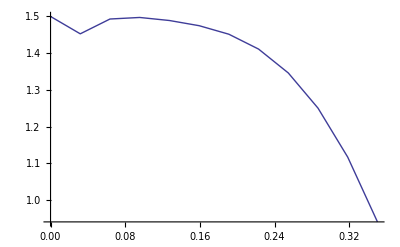

```mathematica
ListPlot[{1/π#⟦1⟧,First[Dm.#⟦2⟧]}&/@ex1,Joined->True]
```

```mathematica
Timing[ex2=evolveRK4[1/100,15/10 π,4/5 zlist^4 Sin[8zlist]];]
```

$Aborted

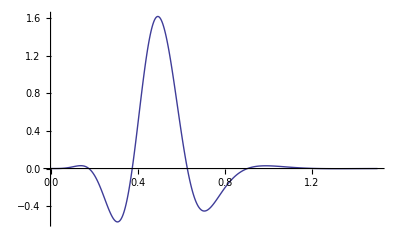

```mathematica
ListPlot[{1/π#⟦1⟧,First[Dm.#⟦2⟧]}&/@ex2,Joined->True,PlotRange->All]
```

```mathematica
Timing[ex3=evolveRK4[1/100,150/10 π,5 zlist Exp[-(zlist-1/4)^2/(15/100)^2]];]
```

{105.80982699999999852,Null}

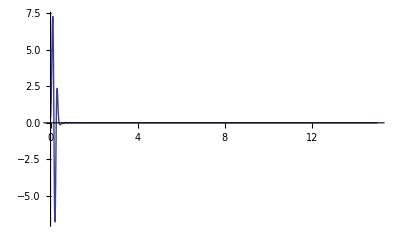

```mathematica
ListPlot[{1/π#⟦1⟧,First[Dm.#⟦2⟧]}&/@ex3,Joined->True,PlotRange->All]
```

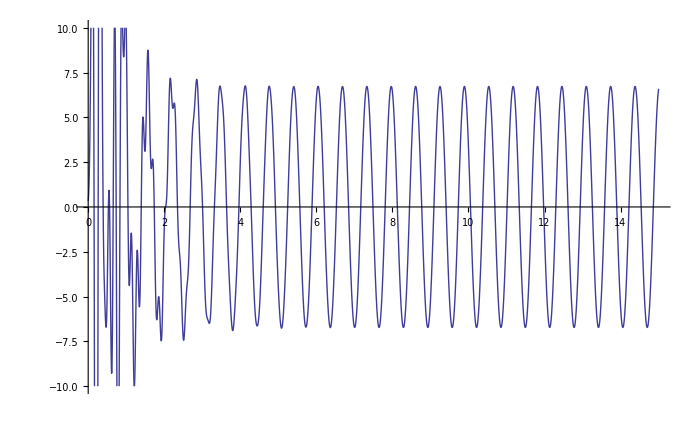

```mathematica
ListPlot[{1/π#⟦1⟧,Exp[2.746676#⟦1⟧]First[Dm.#⟦2⟧]}&/@ex3,Joined->True,PlotRange->{All,{-10,10}}]
```